## README

This notebook contains full calculations for the ω-domain filter functions F_(x,y,z)(ω; Γ)associated with error supression of w.s.s.  noise fields acting (independently) along the three Cartesian (σ_(x,y,z)) directions on the Bloch sphere. These “Cartesian” noise processes correspond to noise in the relaxation (x,y) and dephasing (z) quadratures respectively. F_z(ω; Γ)is the dephasing filter function, as defined in Eq. 13 of Ref. [1]. Also included is the calculation of the filter function F_Ω(ω; Γ), defined in Eq. 14 of Ref. [1], associated with error supression of multuplicative amplitude noise co-axial with the direction of (EQUATORIAL) control. The filter functions are parameterized by a “Γ-matrix” (see below) capturing the user-defined peicewise-constant control protocol. This is consistent with (though generalizes) the notation introudced in Eq. 11 of Ref. [1]. With this formalism, this notebook computes filter functions for “GENERAL” control protocols, as described below. 

GENERAL CONTROL
For GENERAL control protocols, the single-qubit control space is parameterized by the following Γ-matrix formalism 

Γ = (Ω_1 | τ_1 | θ_1 | {n_x^(1),n_y^(1),n_z^(1)}
Ω_2 | τ_2 | θ_2 | {n_x^(2),n_y^(2),n_z^(2)}
. | . | . | .
. | . | . | .
. | . | . | .
Ω_N | τ_N | θ_N | {n_x^(N),n_y^(N),n_z^(N)})

which generically describes any arbitrary N-segment unitary control sequence arising from a piecewise-constant, time-dependent control Hamiltonian (see Eq. 1 of [1] & Eq. 5 of [2]) of the form 

H_c (t)=Σ_(k=1)^N G^(k)(t)Ω_k/2(n̂)^(k).σ̂

where  G^(k)(t) = 1 if t ∈ [t_(k-1,)t_k] and 0 otherwise, and τ_k=t_k-t_(k-1)is the duration of the  kth pulse (beginning at time t_(k-1)and ending at time t_k). The Rabi rate remains constant during eahc individual pulse segment, e.g. taking the value Ω_k during the kth pulse, resulting in a rotation of the Bloch vector through an angle θ_k = Ω_k τ_k, about an axis in Bloch sphere described by the unit vector  (n̂)^(k)= (n_x^(k),n_y^(k),n_z^(k)). Consequently, the form of the Γ matrix captures any possible sequence of (finite-duration) rotations of the Bloch vector, corresponding to any sequence of finite-duration pulsed (unitary) operations on a single qubit. 

Expressed in Mathematica code, we therefore have the following mapping from Hamiltonian control variables to elements of the Γ matrix, 

Ω_k = Γ[[k,1]]
τ_k = Γ[[k,2]]
θ_l = Γ[[k,3]] = Γ[[k,1]]Γ[[k,2]] = Ω_k τ_k 
(n̂)^(k) = Γ[[k,4]]
n_x^(k)= Γ[[k,4]][[1]]
n_y^(k)= Γ[[k,4]][[2]]
n_z^(k)= Γ[[k,4]][[3]]

This arbitrary form of piece-wise constant control is termed GENERAL control throughout these notebooks. Other simpler forms of control, such as EQUATORIAL or SINGLE-AXIS control, are special cases of GENERAL control (see next). 
EQUATORIAL CONTROL:
This corresponds to a piecewise-constant, time-dependent control Hamiltonian, H_c, where in the kth piecewise-constant segment the “direction” of control is specified by a unit vector  (n̂)^(k)= (cos(ϕ_k), sin(ϕ_k), 0) lying in the equatorial plane of the Bloch sphere. The kth pulse segment occurs over the time interval t ∈ [t_(k-1,)t_k], with duration τ_k = t_k-t_(k-1) and Rabi rate Ω_k. Then, during this segment, the control Hamiltonian takes the form  H_c(t∈ [t_(k-1,)t_k]) = Ω_k/2(n̂)^(k).σ̂ =  Ω_k/2[cos(ϕ_k)σ_x+sin(ϕ_k)σ_y], resulting in a rotation of the Bloch vector through an angle θ_k= Ω_k τ_k. Consequently, EQUATORIAL control is a special case of GENERAL control whereby n_x^(k)= cos(ϕ_k), n_y^(k)= sin(ϕ_k)  and  n_z^(k) = 0. This corresponds to driving a qubit with a resonant control field, whose phase during the kth pulse segment is specified by ϕ_k.
SINGLE-AXIS CONTROL 
This corresponds to a piecewise-constant, time-dependent control Hamiltonian, H_c, where in the kth piecewise-constant segment the “direction” of control is fixed by e.g. a unit vector  (n̂)^(k)= (1, 0, 0) lying always long  σ_x. The control Hamiltonian during the kth pulse segment therefore takes the form  H_c(t∈ [t_(k-1,)t_k]) = Ω_k/2 σ_x, resulting in a rotation of the Bloch vector through an angle θ_k= Ω_k τ_k about σ_x. Consequently, SINGEL-AXIS control is a special case of GENERAL control in which n_x^(k)= constant for all k.

[1] H. Ball and M. J. Biercuk, “Walsh-synthesized noise-filtering quantum logic,” arXiv:1410.1624, EPJ Quantum Technology 2, 1 (2015).
[2] Todd J. Green, Jarrah Sastrawan, Hermann Uys, and M.J. Biercuk, “Arbitrary quantum control of qubits in the presence of universal noise.”  New Journal of Physics 15, 095004 (2013).
[3] H. Ball, W. D. Oliver, and M. J. Biercuk, “Upper bounds on qubit coherence set by master clock instabilities,” arXiv:1602.04551 (2016).
[4] A. Soare, H. Ball, D. Hayes, X. Zhen, M. C. Jarratt, H. Uys, and  M.J. Biercuk, “Experimental bath engineering for quantitative studies of quantum control” arXiv:1403.4632 (2014).  Phys. Rev. A. 89, 042329 (2014).

## INITIALIZE SCRIPT

Clear all variables & establish global assumptions

```mathematica
ClearSystemCache[]
Quit[]

ClearAll["Global`*"]
$Assumptions = {
ω,T,n,θ,α,A,B,θ,Y,Δ,δ,Ω,
}∈Reals ;

Simplify[Ω∈Reals]
```

## Γ-MATRIX LIBRARY:

In this section, the user defines the peicewise-constant control protocol in the form of unique Γ matrix, following the notation introudced in Eq. 11 of Ref. [1]. All Γ matrices are to take the following standard form

Γ = (Ω_1 | τ_1 | θ_1 | {n_x^(1),n_y^(1),n_z^(1)}
Ω_2 | τ_2 | θ_2 | {n_x^(2),n_y^(2),n_z^(2)}
. | . | . | .
. | . | . | .
. | . | . | .
Ω_N | τ_N | θ_N | {n_x^(N),n_y^(N),n_z^(N)})
See above for details.

### BB1 Sequence

```mathematica
BB1[θ_,pitime_]:=Join[
{{π/pitime,θ pitime/π,θ,{1,0,0}}},
{{π/pitime,π pitime/π,π,{Cos[ArcCos[-θ/(4π)]],Sin[ArcCos[-θ/(4π)]],0}}},
{{π/pitime,2π pitime/π,2π,{Cos[3ArcCos[-θ/(4π)]],Sin[3ArcCos[-θ/(4π)]],0}}},
{{π/pitime,π pitime/π,π,{Cos[ArcCos[-θ/(4π)]],Sin[ArcCos[-θ/(4π)]],0}}}
];

BB1[θ,Subscript[τ,π]]//MatrixForm
```

(π/τ_π | (θ τ_π)/π | θ | {1,0,0}
π/τ_π | τ_π | π | {-θ/(4 π),√(1-θ^2/(16 π^2)),0}
π/τ_π | 2 τ_π | 2 π | {Cos[3 ArcCos[-θ/(4 π)]],Sin[3 ArcCos[-θ/(4 π)]],0}
π/τ_π | τ_π | π | {-θ/(4 π),√(1-θ^2/(16 π^2)),0})

### DCG Sequence

```mathematica
DCG[pitime_]:=Join[
{{π/pitime, pitime,π,{1,0,0}}},
{{π/(2 pitime), 2pitime,π,{1,0,0}}},
{{π/pitime, pitime,π,{1,0,0}}}
];

DCG[Subscript[τ,π]]//MatrixForm
```

(π/τ_π | τ_π | π | {1,0,0}
π/(2 τ_π) | 2 τ_π | π | {1,0,0}
π/τ_π | τ_π | π | {1,0,0})

### PRIMITIVE X_θ pulse

```mathematica
PRIM[θ_,pitime_]:=Join[
{{π/pitime, θ pitime/π,θ,{1,0,0}}}
];

PRIM[θ,Subscript[τ,π]]//MatrixForm
```

(π/τ_π | (θ τ_π)/π | θ | {1,0,0})

### DUMMY Γ-MATRIX

```mathematica
DUMMY= Table[{Subscript[Ω,i],Subscript[τ,i],Subscript[θ,i], {Subscript[nx,i], Subscript[ny,i], Subscript[nz,i]}},{i,1,3}];
DUMMY//MatrixForm
```

(Ω_1 | τ_1 | θ_1 | {nx_1,ny_1,nz_1}
Ω_2 | τ_2 | θ_2 | {nx_2,ny_2,nz_2}
Ω_3 | τ_3 | θ_3 | {nx_3,ny_3,nz_3})

## CALL Γ-MATRIX

For the purposes of subsequent calculations, define the Γ matrix, together with appropriate experimental parameters, according to one of the pre-defined forms in the Γ-matrix library above. From this point on, the symbol “Γ” is reserved.

```mathematica
pitime=1/5;(*50*10^-6; *)
Γ = DUMMY
Γ//MatrixForm
NumSegments = Length[Γ];
```

{{Ω_1,τ_1,θ_1,{nx_1,ny_1,nz_1}},{Ω_2,τ_2,θ_2,{nx_2,ny_2,nz_2}},{Ω_3,τ_3,θ_3,{nx_3,ny_3,nz_3}}}

(Ω_1 | τ_1 | θ_1 | {nx_1,ny_1,nz_1}
Ω_2 | τ_2 | θ_2 | {nx_2,ny_2,nz_2}
Ω_3 | τ_3 | θ_3 | {nx_3,ny_3,nz_3})

### Pulse boundary times [t_(k-1,)t_k]

```mathematica
PCBinitial[k_,Γ_]:=Sum[Γ[[j,2]],{j,1,k-1}]
PCBfinal[k_,Γ_]:=Sum[Γ[[j,2]],{j,1,k}]
```

## FILTER FUNCTION

Construct pulse-sequence operators, matrices and functions for filter function calculations

### Completed-pulse operator

```mathematica
P[k_,Γ_]:=MatrixExp[-ⅈ(Γ[[k,1]]Γ[[k,2]])/2(Γ[[k,4]][[1]] PauliMatrix[1]+Γ[[k,4]][[2]] PauliMatrix[2]+Γ[[k,4]][[3]] PauliMatrix[3])]
```

### Cumulative operator

See Eq. 8 of Ref. [1]

```mathematica
Q[k_,Γ_]:= Fold[Dot,IdentityMatrix[2],With[{NumProd=k},Table[P[k+1-i,Γ],{i,NumProd}]]]
```

### History Matrix

See Eq. 80 of Ref. [1]

```mathematica
Λelement[k_,Γ_,i_,j_]:=1/2 Tr[ConjugateTranspose[Q[k,Γ]].PauliMatrix[i].Q[k,Γ].PauliMatrix[j]]//ComplexExpand;

Λ[k_,Γ_]:=Table[Λelement[k,Γ,i,j],{i,3},{j,3}];
```

### ω-domain local control-matrix elements

See functions defined in section “GENERAL CONTROL: ω-domain local control-matrix elements stored as functions” of [H.Ball 2016] local_control_matrix_elements_derivation (MASTER).nb. In these formulae, the following substitutions have been made:

Ω = Γ[[k,1]]
τ = Γ[[k,2]]
nx= Γ[[k,4]][[1]]
ny= Γ[[k,4]][[2]]
nz= Γ[[k,4]][[3]]

Using these substitutions, we obtain the following expressions (parameterized by Γ) for the ω-domain local control-matrix elements during the “kth“ pulse assuming GENERAL control.

#### First Row

```mathematica
RxxPlωGENERAL[ω_,k_,Γ_]:=1/(ω^2-Γ[[k,1]]^2)(ω^2-Γ[[k,1]]^2+(Γ[[k,4]][[2]])^2 Γ[[k,1]]^2+(Γ[[k,4]][[3]])^2 Γ[[k,1]]^2+ⅇ^(ⅈ Γ[[k,2]] ω) ((-1+(Γ[[k,4]][[2]])^2+(Γ[[k,4]][[3]])^2) (ω^2-Γ[[k,1]]^2)+((Γ[[k,4]][[2]])^2+(Γ[[k,4]][[3]])^2) ω (-ω Cos[Γ[[k,2]] Γ[[k,1]]]+ⅈ Γ[[k,1]] Sin[Γ[[k,2]] Γ[[k,1]]])))

RxyPlωGENERAL[ω_,k_,Γ_]:=1/(ω^2-Γ[[k,1]]^2)(-Γ[[k,1]] (ⅈ Γ[[k,4]][[3]] ω+Γ[[k,4]][[1]] Γ[[k,4]][[2]] Γ[[k,1]])+ⅇ^(ⅈ Γ[[k,2]] ω) (Γ[[k,4]][[1]] Γ[[k,4]][[2]] (-ω^2+Γ[[k,1]]^2)+ω (Γ[[k,4]][[1]] Γ[[k,4]][[2]] ω+ⅈ Γ[[k,4]][[3]] Γ[[k,1]]) Cos[Γ[[k,2]] Γ[[k,1]]]+ω (Γ[[k,4]][[3]] ω-ⅈ Γ[[k,4]][[1]] Γ[[k,4]][[2]] Γ[[k,1]]) Sin[Γ[[k,2]] Γ[[k,1]]]))

RxzPlωGENERAL[ω_,k_,Γ_]:=1/(ω^2-Γ[[k,1]]^2)(ⅈ Γ[[k,4]][[2]] ω Γ[[k,1]]-Γ[[k,4]][[1]] Γ[[k,4]][[3]] Γ[[k,1]]^2+ⅇ^(ⅈ Γ[[k,2]] ω) (Γ[[k,4]][[1]] Γ[[k,4]][[3]] (-ω^2+Γ[[k,1]]^2)+ω (Γ[[k,4]][[1]] Γ[[k,4]][[3]] ω-ⅈ Γ[[k,4]][[2]] Γ[[k,1]]) Cos[Γ[[k,2]] Γ[[k,1]]]-ω (Γ[[k,4]][[2]] ω+ⅈ Γ[[k,4]][[1]] Γ[[k,4]][[3]] Γ[[k,1]]) Sin[Γ[[k,2]] Γ[[k,1]]]))
```

#### Second Row

```mathematica
RyxPlωGENERAL[ω_,k_,Γ_]:=1/(ω^2-Γ[[k,1]]^2)(ⅈ Γ[[k,4]][[3]] ω Γ[[k,1]]-Γ[[k,4]][[1]] Γ[[k,4]][[2]] Γ[[k,1]]^2+ⅇ^(ⅈ Γ[[k,2]] ω) (Γ[[k,4]][[1]] Γ[[k,4]][[2]] (-ω^2+Γ[[k,1]]^2)+ω (Γ[[k,4]][[1]] Γ[[k,4]][[2]] ω-ⅈ Γ[[k,4]][[3]] Γ[[k,1]]) Cos[Γ[[k,2]] Γ[[k,1]]]-ω (Γ[[k,4]][[3]] ω+ⅈ Γ[[k,4]][[1]] Γ[[k,4]][[2]] Γ[[k,1]]) Sin[Γ[[k,2]] Γ[[k,1]]]))

RyyPlωGENERAL[ω_,k_,Γ_]:=1/(ω^2-Γ[[k,1]]^2)(ω^2-(Γ[[k,4]][[2]])^2 Γ[[k,1]]^2+ⅇ^(ⅈ Γ[[k,2]] ω) ((Γ[[k,4]][[2]])^2 (-ω^2+Γ[[k,1]]^2)+(-1+(Γ[[k,4]][[2]])^2) ω (ω Cos[Γ[[k,2]] Γ[[k,1]]]-ⅈ Γ[[k,1]] Sin[Γ[[k,2]] Γ[[k,1]]])))

RyzPlωGENERAL[ω_,k_,Γ_]:=1/(ω^2-Γ[[k,1]]^2)(-Γ[[k,1]] (ⅈ Γ[[k,4]][[1]] ω+Γ[[k,4]][[2]] Γ[[k,4]][[3]] Γ[[k,1]])+ⅇ^(ⅈ Γ[[k,2]] ω) (Γ[[k,4]][[2]] Γ[[k,4]][[3]] (-ω^2+Γ[[k,1]]^2)+ω (Γ[[k,4]][[2]] Γ[[k,4]][[3]] ω+ⅈ Γ[[k,4]][[1]] Γ[[k,1]]) Cos[Γ[[k,2]] Γ[[k,1]]]+ω (Γ[[k,4]][[1]] ω-ⅈ Γ[[k,4]][[2]] Γ[[k,4]][[3]] Γ[[k,1]]) Sin[Γ[[k,2]] Γ[[k,1]]]))
```

#### Third Row

```mathematica
RzxPlωGENERAL[ω_,k_,Γ_]:=1/(ω^2-Γ[[k,1]]^2)(-Γ[[k,1]] (ⅈ Γ[[k,4]][[2]] ω+Γ[[k,4]][[1]] Γ[[k,4]][[3]] Γ[[k,1]])+ⅇ^(ⅈ Γ[[k,2]] ω) (Γ[[k,4]][[1]] Γ[[k,4]][[3]] (-ω^2+Γ[[k,1]]^2)+ω (Γ[[k,4]][[1]] Γ[[k,4]][[3]] ω+ⅈ Γ[[k,4]][[2]] Γ[[k,1]]) Cos[Γ[[k,2]] Γ[[k,1]]]+ω (Γ[[k,4]][[2]] ω-ⅈ Γ[[k,4]][[1]] Γ[[k,4]][[3]] Γ[[k,1]]) Sin[Γ[[k,2]] Γ[[k,1]]]))

RzyPlωGENERAL[ω_,k_,Γ_]:=1/(ω^2-Γ[[k,1]]^2)(ⅈ Γ[[k,4]][[1]] ω Γ[[k,1]]-Γ[[k,4]][[2]] Γ[[k,4]][[3]] Γ[[k,1]]^2+ⅇ^(ⅈ Γ[[k,2]] ω) (Γ[[k,4]][[2]] Γ[[k,4]][[3]] (-ω^2+Γ[[k,1]]^2)+ω (Γ[[k,4]][[2]] Γ[[k,4]][[3]] ω-ⅈ Γ[[k,4]][[1]] Γ[[k,1]]) Cos[Γ[[k,2]] Γ[[k,1]]]-ω (Γ[[k,4]][[1]] ω+ⅈ Γ[[k,4]][[2]] Γ[[k,4]][[3]] Γ[[k,1]]) Sin[Γ[[k,2]] Γ[[k,1]]]))

RzzPlωGENERAL[ω_,k_,Γ_]:=1/(ω^2-Γ[[k,1]]^2)(ω^2-(Γ[[k,4]][[3]])^2 Γ[[k,1]]^2+ⅇ^(ⅈ Γ[[k,2]] ω) ((Γ[[k,4]][[3]])^2 (-ω^2+Γ[[k,1]]^2)+(-1+(Γ[[k,4]][[3]])^2) ω (ω Cos[Γ[[k,2]] Γ[[k,1]]]-ⅈ Γ[[k,1]] Sin[Γ[[k,2]] Γ[[k,1]]])))
```

### ω-domain local control vectors

#### Cartesian noise terms

Assemble the above matrix elements into vectors associated with calculating filter function in the x, y (relaxation) & z (dephasing) quadratures

```mathematica
RxPlωVECTOR[ω_,k_,Γ_]:={RxxPlωGENERAL[ω,k,Γ],RxyPlωGENERAL[ω,k,Γ],RxzPlωGENERAL[ω,k,Γ]}
RyPlωVECTOR[ω_,k_,Γ_]:={RyxPlωGENERAL[ω,k,Γ],RyyPlωGENERAL[ω,k,Γ],RyzPlωGENERAL[ω,k,Γ]}
RzPlωVECTOR[ω_,k_,Γ_]:={RzxPlωGENERAL[ω,k,Γ],RzyPlωGENERAL[ω,k,Γ],RzzPlωGENERAL[ω,k,Γ]}
```

#### Co-axial noise terms

Define the “Projection Vector” (see Eq.18 of Ref. [1]). The Projection Vector is the vector-class object (equivalent to the ω-domain local control vectors above) for computing filter functions for error suppression of noise in the multuplicative daming quadrature coaxial with control.

```mathematica
ProjVec[k_,Γ_]:= Γ[[k,1]]/2{Γ[[k,4]][[1]],Γ[[k,4]][[2]],0};
```

### ω-domain total control vectors

#### Cartesian noise terms

Following Eq. 127 of Ref. [1] construct the ω-domain total control vectors for computing filter functions in the x, y & z quadratures

```mathematica
RxωVECTOR[ω_,Γ_]:=Sum[Exp[ⅈ* ω*Sum[Γ[[j,2]],{j,1,k-1}]]*RxPlωVECTOR[ω,k,Γ].Λ[k-1,Γ],{k,Length[Γ]}]
RyωVECTOR[ω_,Γ_]:=Sum[Exp[ⅈ* ω*Sum[Γ[[j,2]],{j,1,k-1}]]*RyPlωVECTOR[ω,k,Γ].Λ[k-1,Γ],{k,Length[Γ]}]
RzωVECTOR[ω_,Γ_]:=Sum[Exp[ⅈ* ω*Sum[Γ[[j,2]],{j,1,k-1}]]*RzPlωVECTOR[ω,k,Γ].Λ[k-1,Γ],{k,Length[Γ]}]
```

#### Co-axial noise terms

Following Eq. 16 of Ref. [1] construct the ω-domain total control vectors for computing the filter functions associated with noise in the co-axial (multuplicative daming) quadrature

```mathematica
ExpβΩFactor[ω_,k_,Γ_]:= (Exp[ⅈ* ω*PCBinitial[k,Γ]]-Exp[ⅈ* ω*PCBfinal[k,Γ]]);
RΩωVECTOR[ω_,Γ_]:=Sum[ExpβΩFactor[ω,k,Γ]*ProjVec[k,Γ].Λ[k-1,Γ],{k,Length[Γ]}]
```

### FILTER FUNCTIONS:

#### Relaxation along σ_x axis

```mathematica
Fx[ω_,Γ_]:=Re[RxωVECTOR[ω,Γ].Conjugate[RxωVECTOR[ω,Γ]]]
```

#### Relaxation along σ_y axis

```mathematica
Fy[ω_,Γ_]:=Re[RyωVECTOR[ω,Γ].Conjugate[RyωVECTOR[ω,Γ]]]
```

#### Dephasing

```mathematica
Fz[ω_,Γ_]:=Re[RzωVECTOR[ω,Γ].Conjugate[RzωVECTOR[ω,Γ]]]
```

#### Multuplicative amplitude damping - coaxial with (EQUATORIAL) control

```mathematica
FΩ[ω_,Γ_]:=Re[RΩωVECTOR[ω,Γ].Conjugate[RΩωVECTOR[ω,Γ]]]
```

## PLOT FILTER FUNCTIONS

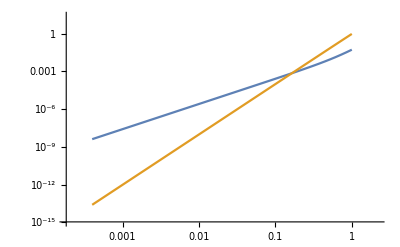

```mathematica
LogLogPlot[{Fz[ω,BB1[π,1/4]//N],FΩ[ω,BB1[π,1/4]//N]},{ω,0.0004,1}]
```

```mathematica
RxPlωMATRIX[ω_,k_,Γ_]:={RxPlωVECTOR[ω,k,Γ],RyPlωVECTOR[ω,k,Γ],RzPlωVECTOR[ω,k,Γ]};
RxPlωMATRIX[0.001,2,DCG[1/4]]//MatrixForm//N
```

(1.25×10^-7-0.0005 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -5.06606×10^-8-1.26651×10^-11 ⅈ | -7.95775×10^-8+0.00031831 ⅈ
0.+0. ⅈ | 7.95775×10^-8-0.00031831 ⅈ | -5.06606×10^-8-1.26651×10^-11 ⅈ)